### PARAMETRES

```mathematica
ClearAll;
```

```mathematica
listH ={200,500,500}; (*мощности слоев*)
slopes = {0 Degree, 0.9 Degree, -0.3 Degree, -4 Degree} ;(*наклон слоев*)

len = 10000;(*длина профиля*)
dx = 100;(*шаг по профилю*)

hDispersion = 1000;(*степень складчатости нижнего слоя в метрах*)
hTapering =2; (*степень влияния нижнего горизонта на верхние*)

type = -1 ;
listV = {2000, 2000,2000,2000,2000}; (*набор скоростей!!!больше на 1 чем горизонтов*)
```

```mathematica
velocityTrend = 1;(*1 or 0*)
velocityAnomaly =0; (*1 or 0*)
```

```mathematica
wellCount= 10 ;(*кол скважин*)
wellType = "regular"; (*расположение скважин "max","min","regular","random"*)
```

### DEPTH

```mathematica
horizons = BuildDepthSection[listH,slopes,len,dx,hDispersion,hTapering, type][["horizons"]];
table = BuildDepthSection[listH,slopes,len,dx,hDispersion,hTapering, type][["table"]];
optsDepth = {Filling -> Bottom, Frame -> True, ImageSize -> 500,
						PlotLabels -> Map["Hor " <> ToString[#] &, (Range[Length[horizons]] - 1)],
						PlotLabel -> "Depth Section"};
PlotDepthSection[horizons, optsDepth]
```

-Graphics-

### VELOCITY

```mathematica
velModel=BuildVelocitySection[horizons,listV, velocityTrend, velocityAnomaly][["model"]];
datasetVelModel=BuildVelocitySection[horizons,listV, velocityTrend, velocityAnomaly][["dataset"]]
```

Dataset[<>]

```mathematica
optsVel1 = {PlotStyle -> {Directive[Thickness[0.005], Black]},
							PlotLabels -> Map["Hor " <> ToString[#] &, (Range[Length[horizons]] - 1)],
							ImageSize -> 500};
optsVel2 = {ColorFunction -> ColorData[{"RedBlueTones", "Reverse"}],
						PlotLegends -> BarLegend[Automatic, LegendLabel -> "Vel, m/s"],
						PlotLabel -> "Velocity Distribution",
						Contours -> {Automatic, 20}(*,
					GridLines->{DeleteDuplicates[Normal[wellDataset[All, "x"]]], None}*)};
PlotVelocity[velModel, horizons,{optsVel1, optsVel2}]
```

### TIME

```mathematica
time=BuildTimeSection[horizons, velModel][["time"]];
optsTime = {Filling -> Bottom, Frame -> True, ImageSize -> 500,
						PlotLabels -> Map["t " <> ToString[#] &, (Range[Length[time]] - 1)],
						PlotLabel -> "Time Section"};
PlotTimeSection[time, optsTime]
```

-Graphics-

### WELLS

```mathematica
wellDataset = BuildWellSet[horizons, time, wellCount, wellType][["dataset"]];
positions = BuildWellSet[horizons, time,  wellCount, wellType][["positions"]];
PlotDepthSection[horizons, {Filling -> Bottom, Frame -> True, ImageSize -> 500,
						PlotLabels -> Map["Hor " <> ToString[#] &, (Range[Length[horizons]] - 1)],
						PlotLabel -> "Depth Section",GridLines->{DeleteDuplicates[Normal[wellDataset[All, "x"]]], None},											
											PlotLabel -> "Depth Section with wells"}]
```

-Graphics-

```mathematica
PlotTimeSection[time, {GridLines->{DeleteDuplicates[Normal[wellDataset[All, "x"]]], None},
					    Filling -> Bottom, Frame -> True, ImageSize -> 500,
						PlotLabels -> Map["t " <> ToString[#] &, (Range[Length[time]] - 1)],
						PlotLabel -> "Time Section with Wells"
}]
```

-Graphics-

```mathematica
|
```

### CheckVelocity

```mathematica
datasetVint= CheckVelocity[wellDataset][["dataset"]]
```

### HTMethod

{FittedModel[76.0808+3661.88 t],FittedModel[-175.248+3926.78 t],FittedModel[-190.224+3981.64 t],FittedModel[1258.13+2209.76 t]}

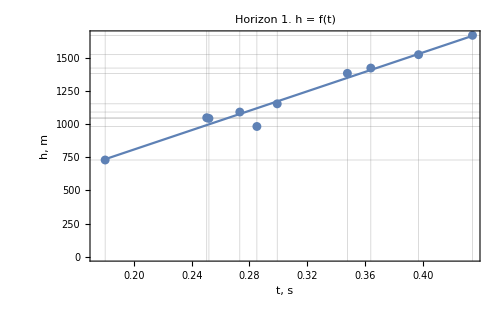
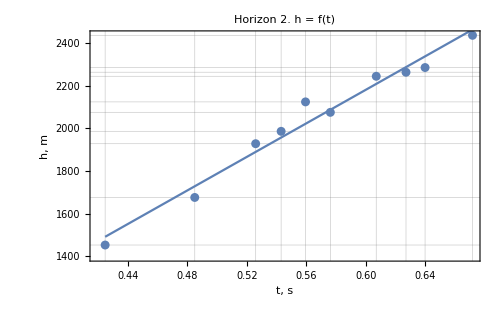
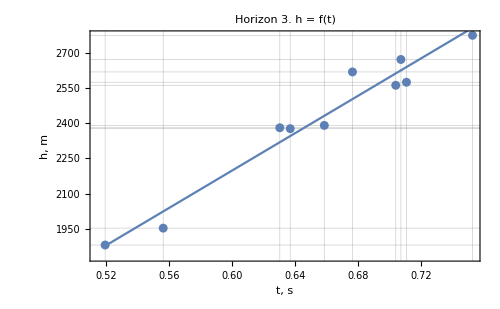
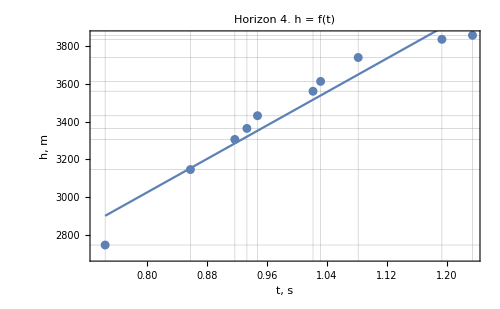

```mathematica
Clear[t];
lmSetHT=HTMethod[wellDataset,time, t][["lmSet"]]
lmParametresHT=HTMethod[wellDataset, time, t][["lmParametres"]];
resultHT=HTMethod[wellDataset, time, t][["result"]];
wellValuesHT=HTMethod[wellDataset, time, t][["wellValues"]];
PlotHT[wellValuesHT,lmSetHT, t]
```

### VTMethod

{FittedModel[4217.59-948.856 t],FittedModel[3205.6+715.709 t],FittedModel[3333.03+540.863 t],FittedModel[4707.78-1215.33 t]}

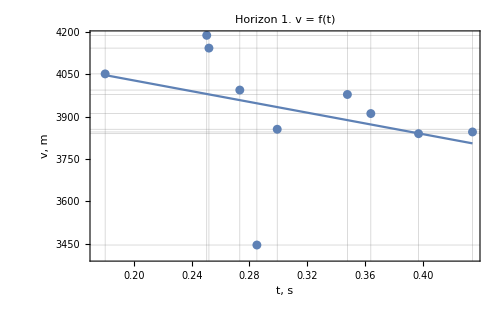
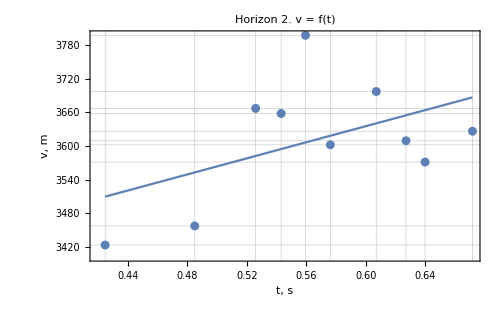
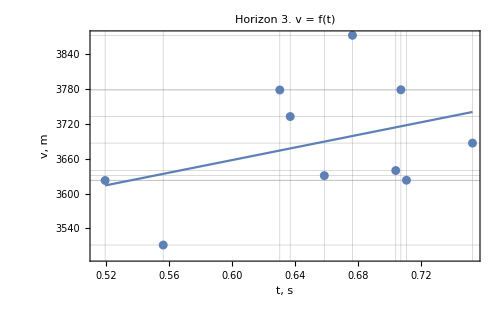
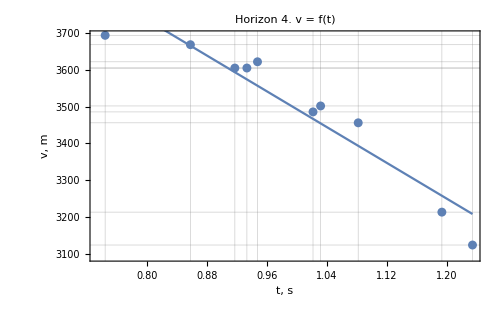

```mathematica
lmSetVT=VTMethod[wellDataset,time, t][["lmSet"]]
lmParametresVT=VTMethod[wellDataset,time, t][["lmParametres"]];
wellValuesVT=VTMethod[wellDataset,time, t][["wellValues"]];
resultVT = VTMethod[wellDataset, time, t][["result"]];
fitsVT = VTMethod[wellDataset, time, t][["fits"]];
PlotVT[wellValuesVT,lmSetVT, t]
```

### THMethod

{FittedModel[-0.00919763+0.000263477 h],FittedModel[0.0591828+0.000247555 h],FittedModel[0.0747477+0.000239999 h],FittedModel[-0.466516+0.00042281 h]}

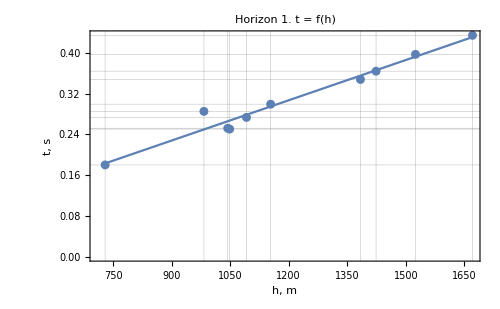
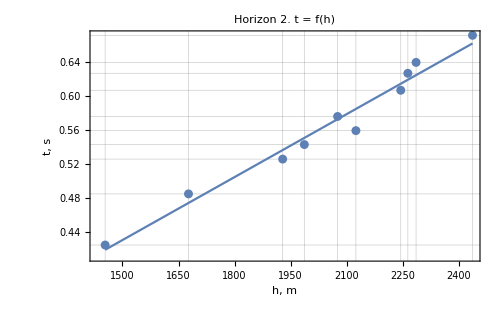
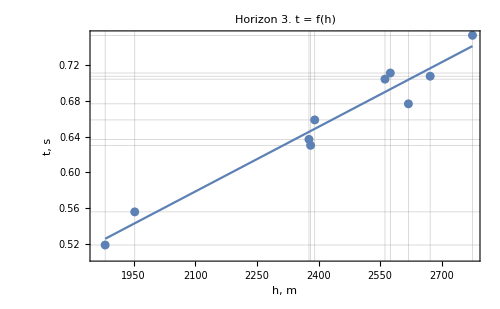
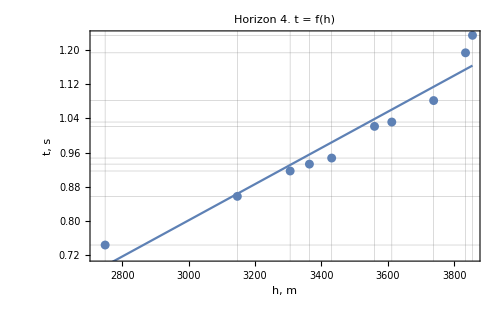

```mathematica
Clear[h];
lmSetTH=THMethod[wellDataset,time, h][["lmSet"]]
lmParametresTH=THMethod[wellDataset, time, h][["lmParametres"]];
wellValuesTH = THMethod[wellDataset, time, h][["wellValues"]];
resultTH=THMethod[wellDataset, time, h][["result"]];
PlotTH[wellValuesTH,lmSetTH, h]
```

### VaveMethod

```mathematica
vAveTable=VaveMethod[wellDataset,time][["vAveTable"]]
resultVave=VaveMethod[wellDataset, time][["result"]];
fitsVave = VaveMethod[wellDataset, time][["fits"]]
```

{3924.99,3610.76,3687.37,3497.17}

{{{0,-120.057},{100,-437.483},{200,-743.159},{300,-1001.72},{400,-1119.29},{500,-1081.02},{600,-991.441},{700,-943.385},{800,-930.87},{900,-911.611},{1000,-949.136},{1100,-977.682},{1200,-980.839},{1300,-1053.65},{1400,-1174.56},{1500,-1322.11},{1600,-1504.85},{1700,-1638.08},{1800,-1712.41},{1900,-1774.05},{2000,-1766.38},{2100,-1702.29},{2200,-1592.2},{2300,-1502.38},{2400,-1428.88},{2500,-1370.62},{2600,-1448.99},{2700,-1556.68},{2800,-1685.14},{2900,-1688.22},{3000,-1625.15},{3100,-1526.24},{3200,-1451.01},{3300,-1549.67},{3400,-1705.15},{3500,-1936.65},{3600,-2170.66},{3700,-2218.52},{3800,-2110.46},{3900,-1872.02},{4000,-1578.78},{4100,-1275.35},{4200,-1078.19},{4300,-976.661},{4400,-983.003},{4500,-1114.73},{4600,-1336.16},{4700,-1633.3},{4800,-1857.78},{4900,-1970.47},{5000,-1974.57},{5100,-1880.05},{5200,-1816.68},{5300,-1678.12},{5400,-1558.59},{5500,-1500.02},{5600,-1467.45},{5700,-1332.07},{5800,-1164.17},{5900,-1009.56},{6000,-920.148},{6100,-824.489},{6200,-815.1},{6300,-857.487},{6400,-1072.88},{6500,-1370.6},{6600,-1568.37},{6700,-1688.38},{6800,-1758.54},{6900,-1615.16},{7000,-1490.63},{7100,-1307.22},{7200,-1282.85},{7300,-1290.01},{7400,-1365.2},{7500,-1461.74},{7600,-1577.27},{7700,-1696.39},{7800,-1704.73},{7900,-1622.39},{8000,-1551.71},{8100,-1345.78},{8200,-1163.85},{8300,-1012.23},{8400,-988.985},{8500,-1056.28},{8600,-1196.54},{8700,-1398.25},{8800,-1506.21},{8900,-1513.24},{9000,-1337.69},{9100,-1089.87},{9200,-882.009},{9300,-778.703},{9400,-707.005},{9500,-725.163},{9600,-747.898},{9700,-713.11},{9800,-573.087},{9900,-438.024},{10000,-302.678}},{{0,-1075.7},{100,-1173.32},{200,-1300.57},{300,-1435.04},{400,-1533.33},{500,-1576.62},{600,-1599.33},{700,-1621.01},{800,-1638.83},{900,-1653.92},{1000,-1679.53},{1100,-1713.37},{1200,-1755.48},{1300,-1818.99},{1400,-1899.21},{1500,-1990.07},{1600,-2090.12},{1700,-2175.06},{1800,-2234.44},{1900,-2278.21},{2000,-2289.59},{2100,-2274.95},{2200,-2242.78},{2300,-2215.78},{2400,-2192.39},{2500,-2176.35},{2600,-2188.24},{2700,-2215.57},{2800,-2258.17},{2900,-2275.02},{3000,-2280.61},{3100,-2288.78},{3200,-2311.68},{3300,-2365.51},{3400,-2426.35},{3500,-2501.98},{3600,-2580.26},{3700,-2584.24},{3800,-2512.25},{3900,-2384.87},{4000,-2248.17},{4100,-2131.47},{4200,-2057.43},{4300,-2020.41},{4400,-2020.44},{4500,-2059.09},{4600,-2135.94},{4700,-2255.18},{4800,-2372.67},{4900,-2454.71},{5000,-2489.66},{5100,-2478.18},{5200,-2450.75},{5300,-2387.88},{5400,-2311.06},{5500,-2231.33},{5600,-2149.54},{5700,-2050.98},{5800,-1957.65},{5900,-1886.43},{6000,-1844.29},{6100,-1830.78},{6200,-1847.97},{6300,-1892.89},{6400,-1961.15},{6500,-2062.18},{6600,-2162.05},{6700,-2238.12},{6800,-2289.31},{6900,-2276.53},{7000,-2263.49},{7100,-2246.52},{7200,-2244.14},{7300,-2248.94},{7400,-2264.69},{7500,-2287.11},{7600,-2312.9},{7700,-2337.07},{7800,-2328.39},{7900,-2290.38},{8000,-2245.3},{8100,-2179.18},{8200,-2128.82},{8300,-2096.48},{8400,-2080.79},{8500,-2075.91},{8600,-2083.25},{8700,-2106.22},{8800,-2119.97},{8900,-2103.48},{9000,-2042.14},{9100,-1971.},{9200,-1902.52},{9300,-1828.77},{9400,-1751.13},{9500,-1668.76},{9600,-1593.21},{9700,-1524.78},{9800,-1462.52},{9900,-1411.24},{10000,-1373.27}},{{0,-1579.26},{100,-1639.1},{200,-1731.52},{300,-1836.67},{400,-1914.43},{500,-1949.69},{600,-1975.27},{700,-2007.97},{800,-2042.65},{900,-2076.12},{1000,-2117.04},{1100,-2159.77},{1200,-2202.58},{1300,-2258.02},{1400,-2323.67},{1500,-2396.65},{1600,-2478.79},{1700,-2549.43},{1800,-2600.7},{1900,-2642.53},{2000,-2657.89},{2100,-2652.53},{2200,-2633.51},{2300,-2618.65},{2400,-2607.47},{2500,-2601.36},{2600,-2619.54},{2700,-2649.53},{2800,-2692.02},{2900,-2704.04},{3000,-2701.34},{3100,-2696.08},{3200,-2702.35},{3300,-2734.51},{3400,-2775.26},{3500,-2835.1},{3600,-2906.1},{3700,-2913.29},{3800,-2856.58},{3900,-2755.46},{4000,-2650.69},{4100,-2566.53},{4200,-2518.28},{4300,-2495.55},{4400,-2493.98},{4500,-2514.19},{4600,-2561.5},{4700,-2643.17},{4800,-2722.65},{4900,-2771.54},{5000,-2781.55},{5100,-2757.},{5200,-2731.03},{5300,-2678.29},{5400,-2620.53},{5500,-2566.54},{5600,-2514.25},{5700,-2444.47},{5800,-2376.27},{5900,-2324.02},{6000,-2292.29},{6100,-2278.5},{6200,-2284.56},{6300,-2307.31},{6400,-2348.13},{6500,-2420.82},{6600,-2493.83},{6700,-2552.22},{6800,-2595.89},{6900,-2583.13},{7000,-2578.29},{7100,-2570.22},{7200,-2576.94},{7300,-2584.07},{7400,-2595.41},{7500,-2609.57},{7600,-2626.01},{7700,-2643.38},{7800,-2634.76},{7900,-2601.84},{8000,-2568.48},{8100,-2514.53},{8200,-2474.96},{8300,-2448.27},{8400,-2428.02},{8500,-2410.12},{8600,-2398.77},{8700,-2401.39},{8800,-2397.2},{8900,-2369.71},{9000,-2303.89},{9100,-2236.47},{9200,-2178.09},{9300,-2115.86},{9400,-2050.49},{9500,-1979.03},{9600,-1913.57},{9700,-1854.51},{9800,-1802.02},{9900,-1760.01},{10000,-1732.02}},{{0,-2937.7},{100,-2982.81},{200,-3057.49},{300,-3145.3},{400,-3207.28},{500,-3231.14},{600,-3249.14},{700,-3276.87},{800,-3307.98},{900,-3341.97},{1000,-3385.},{1100,-3430.85},{1200,-3478.09},{1300,-3536.91},{1400,-3607.17},{1500,-3685.51},{1600,-3773.98},{1700,-3858.01},{1800,-3924.51},{1900,-3990.91},{2000,-4039.17},{2100,-4074.07},{2200,-4097.63},{2300,-4131.82},{2400,-4172.45},{2500,-4218.38},{2600,-4289.7},{2700,-4361.03},{2800,-4434.4},{2900,-4482.65},{3000,-4486.29},{3100,-4429.71},{3200,-4359.21},{3300,-4328.4},{3400,-4315.23},{3500,-4325.67},{3600,-4358.26},{3700,-4335.36},{3800,-4264.84},{3900,-4150.64},{4000,-4038.19},{4100,-3938.55},{4200,-3872.09},{4300,-3820.37},{4400,-3782.46},{4500,-3756.2},{4600,-3751.08},{4700,-3777.51},{4800,-3802.01},{4900,-3802.07},{5000,-3772.13},{5100,-3720.97},{5200,-3678.64},{5300,-3621.11},{5400,-3571.72},{5500,-3529.82},{5600,-3496.3},{5700,-3446.14},{5800,-3397.56},{5900,-3356.63},{6000,-3330.05},{6100,-3310.11},{6200,-3301.96},{6300,-3302.11},{6400,-3312.93},{6500,-3348.54},{6600,-3383.13},{6700,-3402.01},{6800,-3407.15},{6900,-3362.03},{7000,-3328.05},{7100,-3294.43},{7200,-3278.04},{7300,-3266.86},{7400,-3263.48},{7500,-3264.25},{7600,-3268.35},{7700,-3276.18},{7800,-3259.89},{7900,-3220.85},{8000,-3179.81},{8100,-3119.95},{8200,-3071.35},{8300,-3032.75},{8400,-3000.24},{8500,-2969.98},{8600,-2947.09},{8700,-2937.3},{8800,-2924.15},{8900,-2890.66},{9000,-2824.41},{9100,-2760.3},{9200,-2709.29},{9300,-2657.01},{9400,-2602.72},{9500,-2544.43},{9600,-2491.09},{9700,-2442.45},{9800,-2396.96},{9900,-2359.34},{10000,-2331.52}}}

### GRAPHICS

```mathematica
Show[ListLinePlot[horizons, GridLines->{DeleteDuplicates[Normal[wellDataset[All, "x"]]], None},
						Filling -> Bottom, Frame -> True, ImageSize -> 1000,
					PlotLabels -> Map["Hor " <> ToString[#] &, (Range[Length[horizons]] - 1)], PlotStyle->Gray],
	ListLinePlot[resultHT[[2;;-1]], PlotStyle->{Blue}],
	ListLinePlot[resultVT[[2;;-1]] , PlotStyle->{Orange}],
	ListLinePlot[resultTH[[2;;-1]], PlotStyle->{Green}],
ListLinePlot[resultVave[[2;;-1]], PlotStyle->{Red}]
]
```

-Graphics-

```mathematica
PlotDepthSection[resultHT,  GridLines->{DeleteDuplicates[Normal[wellDataset[All, "x"]]], None},
						Filling -> Bottom,  Frame -> True, ImageSize -> 500,
						PlotLabels -> Map["Hor " <> ToString[#] &, (Range[Length[horizons]] - 1)],
						PlotLabel -> "H(t)"]
```

-Graphics-

```mathematica
PlotDepthSection[resultVT ,  GridLines->{DeleteDuplicates[Normal[wellDataset[All, "x"]]], None},
						Filling -> Bottom, Frame -> True, ImageSize -> 500,
						PlotLabels -> Map["Hor " <> ToString[#] &, (Range[Length[horizons]] - 1)],
						PlotLabel -> "V(t)"]
```

-Graphics-

```mathematica
PlotDepthSection[resultTH,  GridLines->{DeleteDuplicates[Normal[wellDataset[All, "x"]]], None},
						Filling -> Bottom,  Frame -> True, ImageSize -> 500,
						PlotLabels -> Map["Hor " <> ToString[#] &, (Range[Length[horizons]] - 1)],
						PlotLabel -> "T(H)"]
```

-Graphics-

```mathematica
PlotDepthSection[resultVave,  GridLines->{DeleteDuplicates[Normal[wellDataset[All, "x"]]], None},
						Filling -> Bottom,  Frame -> True, ImageSize -> 500,
						PlotLabels -> Map["Hor " <> ToString[#] &, (Range[Length[horizons]] - 1)],
						PlotLabel -> "Vave"]
```

-Graphics-